```mathematica
(* Gitterkonstanten in A *)
Subscript[a, InP]=5.8687;
Subscript[a, GaP]=5.4505;
Subscript[a, GaAs]=5.65325;

(* Bandlücke in eV *)
Subscript[Eg, InP][T_]:=1.421 - 4.9*10^-4*T^2/(T+327);
Subscript[Eg, GaP][T_]:=2.34 - 6*10^-4*T^2/(T+460);
Subscript[Eg, InP][300];
Subscript[Eg, GaP][300];
Subscript[Eg, InP][80];
Subscript[Eg, GaP][80];

(* Passe Gitterkonstante an GaAs an *)
Clear[x];
x=First[x/.Solve[Subscript[a, GaAs]==x*Subscript[a, GaP]+(1-x)*Subscript[a, InP],x]];

(* Bandlücke für diese Zusammenensetzung in eV bei 300K *)
Subscript[Eg, misch]=1.351+0.643*x+0.786*x^2;
Subscript[λ, misch]=1240/Subscript[Eg, misch];

(* Bandlücke Zusammensetzung in eV bei 80K aus Wichtung *)
Test = x*Subscript[Eg, GaP][80]+(1-x)*Subscript[Eg, InP][80];
Subscript[Eg, misch80]=x*Subscript[Eg, GaP][80]+(1-x)*Subscript[Eg, InP][80]+(2.01-1.88)
Subscript[λ, misch80]=1240/Subscript[Eg, misch80]
```

2.01706

614.758

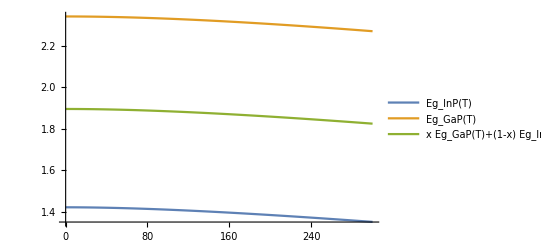

```mathematica
Plot[{Subscript[Eg, InP][T],Subscript[Eg, GaP][T],x*Subscript[Eg, GaP][T]+(1-x)*Subscript[Eg, InP][T]},{T,0,300},PlotLegends->"Expressions"];
```

```mathematica
(* Berechnung Exzitonen bindungungsenergie *)
(* from: http://www.ioffe.ru/SVA/NSM/Semicond/GaInP/basic.html *)
Subscript[E, exi]=1/11^2*(0.08*0.7/(0.08+0.7))/(1836/(1836+1))*13.6
```

0.0080739